```mathematica
N[(π-(3 √3)/4)]
N[(π+(3 √3)/4)]
N[4π(1-.75^2)]
N[π+(3 √3)/4+(3 √3)/(4π)]
```

1.84255

4.44063

5.49779

4.85413

```mathematica
N[(√3)/(4π)]
```

0.137832

```mathematica
N[(√3)/4]
```

0.433013

```mathematica
N[1-(√3)/(4π)]
```

0.862168

```mathematica
Simplify[((1-((√3)/(4π)p)^k)(3/4)(4.8541)p^2)/((1-(√3)/(4π))^k 3p)]
```

-1.21353 p (-√3+4 π)^-k (3^(k/2) p^k-1. (4 π)^k)

```mathematica
N[π*0.01]
```

0.0314159

```mathematica
N[1/(2*300*π*0.01*8)]
```

0.00663146

```mathematica
N[√(1/(4π))]
```

0.282095

```mathematica
Simplify[Solve[(√3)/(4π)*p==P_U*(1-(√3)/(4π))^k+0.175*p*(1-(1-(√3)/(4π))^k), P_U]]
```

{{P_U→(-0.0371678+0.175 0.862168^k) ⅇ^(0.148305 k) p}}

```mathematica
Cos[π/3]
```

1/2

```mathematica
N[(0.1723*0.9777+0.1728*0.9751+0.1596*0.9806+0.1727*0.9912+0.1669*0.9911)/(0.9777+0.9751+0.9806+0.9912+0.9911)]
```

0.168858

```mathematica
Log[1-(√3)/(4π)/0.1689]/Log[1-(√3)/(4π)]
```

11.4165

```mathematica
Solve[0.1689+((√3)/(4π)-0.1689)(1-(√3)/(4π))^-k==0,k]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{k→11.4165}}

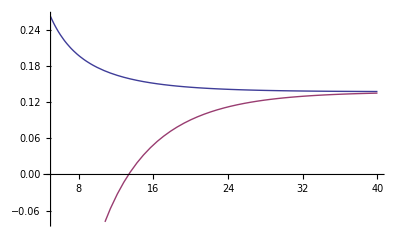

```mathematica
Plot[{(√3)/(4π)/(1-(1-(√3)/(4π))^k),((1-(√3)/(4 π))^k-(√3)/(4 π))/((1-(√3)/(4 π))^k-1)},{k,5,40}]
```

```mathematica
Solve[x^11==0.359,x]
```

{{x→-0.87417-0.256679 ⅈ},{x→-0.87417+0.256679 ⅈ},{x→-0.596627-0.688544 ⅈ},{x→-0.596627+0.688544 ⅈ},{x→-0.129659-0.901801 ⅈ},{x→-0.129659+0.901801 ⅈ},{x→0.378474-0.828743 ⅈ},{x→0.378474+0.828743 ⅈ},{x→0.766445-0.492564 ⅈ},{x→0.766445+0.492564 ⅈ},{x→0.911075}}

```mathematica
Sin[π-θ]
```

Sin[θ]

```mathematica
Gamma[2]
```

1

```mathematica
N[∫_0^(2π/3) (1-(θ-Sin[θ])/π)^k*2/3 Sin[θ]ⅆθ]
```

```mathematica
Plot[∫_0^(2π/3) (1-(θ-Sin[θ])/π)^k*2/3 Sin[θ]ⅆθ, {k,2,10}, PlotPoints->9]
```

$Aborted

```mathematica
N[∫_0^(2π/3) (1-(θ-Sin[θ])/π)^31*2/3 Sin[θ]ⅆθ]
```

45.8561

{{1,0.862168},{2,0.75613},{3,0.673142},{4,0.607086},{5,0.553643},{6,0.509726},{7,0.473108},{8,0.44216},{9,0.41568},{10,0.392767},{11,0.372737},{12,0.355069},{13,0.339355},{14,0.325277},{15,0.31258},{16,0.301063},{17,0.290558},{18,0.280932},{19,0.272072},{20,0.263885},{21,0.256292},{22,0.249233},{23,0.242636},{24,0.236162},{25,0.23446},{26,0.268766},{27,0.0999494},{28,-0.539183},{29,-2.25928},{30,-16.1986},{31,45.8561},{32,-6827.38},{33,3303.08},{34,1.25719×10^6},{35,-1.02244×10^7},{36,1.36386×10^7},{37,2.4582×10^8},{38,2.40977×10^10},{39,-9.983×10^10},{40,-3.29146×10^12}}

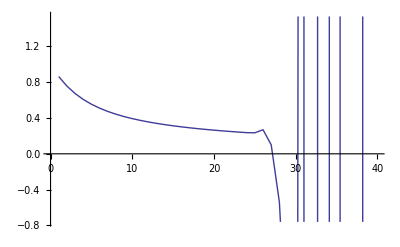

```mathematica
pyx = Table[{k,N[∫_0^(2π/3) (1-(θ-Sin[θ])/π)^k*2/3 Sin[θ]ⅆθ]}, {k,1,40}];
Print[pyx];ListLinePlot[pyx]
```